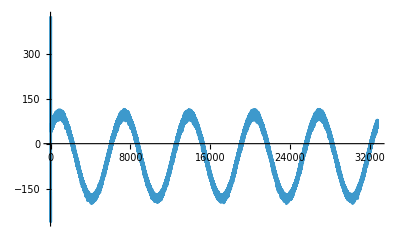

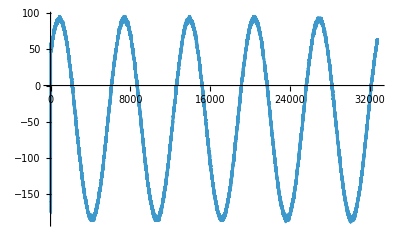

283.202

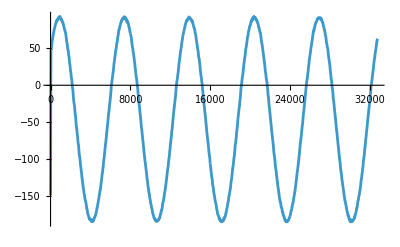

277.922

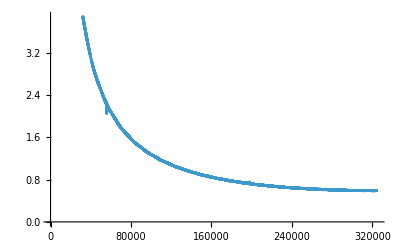

{{10440625/1024,12231.9,4324.64},{20596875/2048,11498.3,4065.26},{21571875/2048,11259.8,3980.93}}

```mathematica
fs=65*10^4;

data=First@Import["/home/shaoyafan/develop/wavegen/raw_adc.txt","CSV"];
n=Length[data];
data=data[[1;;n]];
ListLinePlot[data]
data=MedianFilter[data,7];
ListLinePlot[data]
Max[data]-Min[data]
data=LowpassFilter[data,550000,64,SampleRate->65000000];
ListLinePlot[data]
Max[data]-Min[data]
fft=Fourier[data];
spectrum=Abs[fft];
freq=Range[0,n-1] fs/n;
half=Floor[n/2];
freqHalf=freq[[1;;half]];
specHalf=spectrum[[1;;half]];
band=Pick[Range[Length[freqHalf]],Thread[10000<=freqHalf<=500000]];
freqBand=freqHalf[[band]];
specBand=specHalf[[band]];
ListLinePlot[Transpose[{freqBand,specBand}]]
peaks=FindPeaks[specBand];
peaksSorted=Reverse@SortBy[peaks,Last];
components=Take[peaksSorted,UpTo[3]];
idx=components[[All,1]];
peakFreq=freqBand[[idx]];
peakAmplitude=2 specBand[[idx]] Sqrt[n];
vpp=2 peakAmplitude;
vrms=peakAmplitude/Sqrt[2];
result=Transpose[{peakFreq,vpp,vrms}]
```